## Accelerometer Data

```mathematica
SetDirectory["C:\\Users\\stuma\\Desktop\\Mammut"];
vert=Import["C:\\Users\\stuma\\Desktop\\Mammut\\vertical.txt","Data"];
index=vert[[All,1]];
l1=vert[[All,1;;2]];
l2=Transpose[{index,vert[[All,3]]}];
l3=Transpose[{index,vert[[All,4]]}];
r1=Transpose[{index,vert[[All,5]]}];
r2=Transpose[{index,vert[[All,6]]}];
r3=Transpose[{index,vert[[All,7]]}];
```

Plot x, y, z raw accel data:

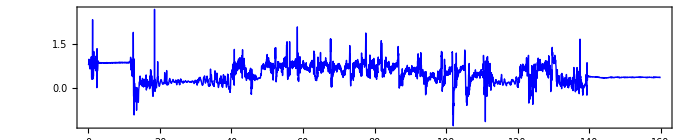

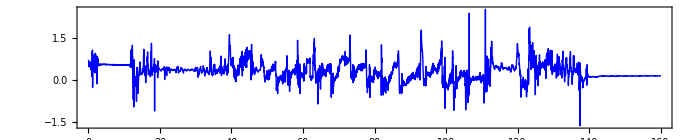

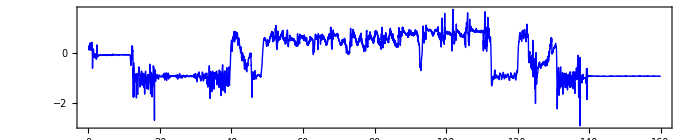

```mathematica
ListPlot[l1[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True]
ListPlot[l2[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True]
ListPlot[l3[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True]
```

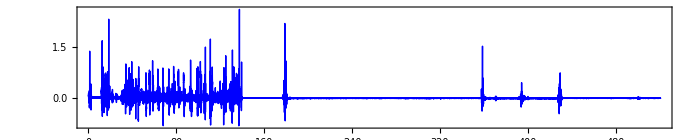

```mathematica
l2a=vert[[All,2;;4]];
l2c=Sqrt[#[[1]]^2+#[[2]]^2+#[[3]]^2]&/@vert[[All,2;;4]];
ListPlot[Transpose[{vert[[All,1]],l2c}][[10000;;12000]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True];
bg=Mean[l2c[[10000;;12000]]];
ListPlot[Transpose[{vert[[All,1]],l2c-bg}],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True]
```

Idea of hand icon moving in response to the accel data:

```mathematica
pts=Dimensions[l2c][[1]];
hand=Quiet@Import["Icons8-Ios7-Hands-Hand.ico"][[6]];

base=Table[RandomReal[],{i,0,10,0.1},{j,0,10,0.1}];

xax=vert[[All,2]][[1;;100]];
yax=vert[[All,3]][[1;;100]];
zax=vert[[All,4]][[1;;100]];
xyax=Transpose[{yax,zax}];
```

```mathematica
hand1=ArrayPlot[base,Frame->True,Epilog->Inset[hand,{50+(10*#[[1]]),50+(10*#[[2]])}],PlotRange->{0,0}]&/@xyax;
```

```mathematica
Export["C:\\Users\\stuma\\Desktop\\Mammut\\hand1.gif",hand1];
```

Extracting more physical data from the raw measurements:

```mathematica
test=ArrayResample[l1[[1;;160*50]],1000];
bs=BSplineFunction[test,SplineDegree->10];
```

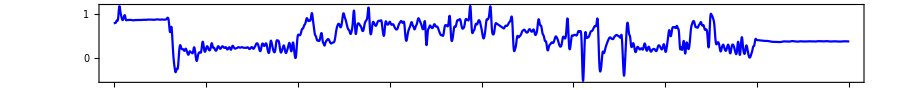

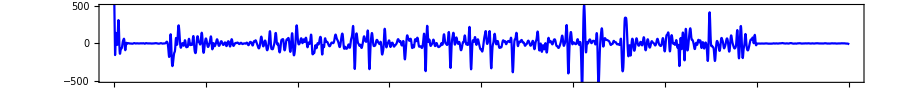

```mathematica
ParametricPlot[bs[u],{u,0,1},AspectRatio->0.1,FrameStyle->Directive[Black,FontFamily->"Calibri",20],Frame->True,Axes->False,PlotRangePadding->None,ImagePadding->{{Automatic, 10}, {Automatic, 10}},PlotStyle->Directive[Blue],ImageSize->900]

Quiet@ParametricPlot[{bs[u][[1]],bs'[u][[2]]},{u,0,1},AspectRatio->0.1,FrameStyle->Directive[Black,FontFamily->"Calibri",20],Frame->True,Axes->False,PlotRange->{All,{-500,500}},PlotRangePadding->None,ImagePadding->{{Automatic, 10}, {Automatic, 10}},PlotStyle->Directive[Blue],ImageSize->900]
```

```mathematica
vel=Table[Total[(l2c-1.04)[[1;;i]]]*0.2,{i,1,10000}];
```

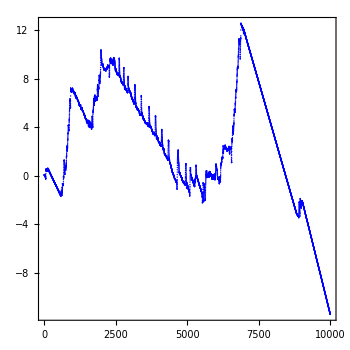

```mathematica
ListPlot[vel]
```

Misc...

```mathematica
(*Import["C:\\Users\\stuma\\Desktop\\Mammut\\filey.csv","Data"]*)
```

```mathematica
(*ListPlot[r1[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True,PlotStyle->Red]
ListPlot[r2[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True,PlotStyle->Red]
ListPlot[r3[[1;;160*50]],AspectRatio->0.2,ImageSize->700,PlotRange->All,Joined->True,PlotStyle->Red]*)
```

## Height tracking

```mathematica
filepath1="C:\\Users\\stuma\\Desktop\\Mammut\\h5file.h5";
filepath2="C:\\Users\\stuma\\Desktop\\Mammut\\h5raw.h5";
Import[filepath1]
Import[filepath1,"Elements"]

Import[filepath2]
```

{/climbs/0/height_profile,/climbs/0/moves_LH,/climbs/0/moves_RH,/climbs/all}

{Annotations,Attributes,Data,DataEncoding,DataFormat,Datasets,Dimensions,Groups}

{/acc_LH,/acc_RH,/button_LH,/button_RH,/classifier_binary,/classifier_original,/classifier_postprocess,/classifier_raw,/climbing,/energy_LH,/energy_RH,/nfc_LH,/nfc_RH,/pres_LH,/pres_RH}

```mathematica
height=Import[filepath1,{"Datasets","/climbs/0/height_profile"}];
Import[filepath1,"Attributes"]
```

{/climbs→{},/climbs/0→{},/climbs/0/height_profile→{},/climbs/0/moves_LH→{},/climbs/0/moves_RH→{},/climbs/all→{}}

```mathematica
Import[filepath1,"Groups"]
```

{/climbs,/climbs/0}

```mathematica
Import[filepath2,"Groups"]
```

{}

```mathematica
dh=Dimensions[height][[1]];
mh=Max[height];
bars=BarChart[{#},PlotRange->{0,mh},Frame->True,Background->None,AspectRatio->5,FrameStyle->Directive[Black,FontFamily->"Calibri",14],ImageSize->100,ChartStyle->RGBColor[0,0,1,0.4],PlotRangePadding->None]&/@(height[[1;;100]]);
```

```mathematica
Export["C:\\Users\\stuma\\Desktop\\Mammut\\bars.gif",bars];
```

```mathematica
step=Table[i,{i,0,dh-1}];
lis=Transpose[{step,height}];

gif2=Table[ListPlot[lis[[1;;i]],Joined->True,PlotRange->{{0,dh},{0,mh}},PlotRangePadding->None,ImagePadding->{{Automatic, 10}, {Automatic, 10}},FrameLabel->{"Step","Height (m)"},Background->None],{i,1,300}];
gif3=Table[ListPlot[lis[[1;;i]],Joined->True,PlotRange->{{0,dh},{0,mh}},PlotRangePadding->None,ImagePadding->{{Automatic, 10}, {Automatic, 10}},FrameLabel->{"Step","Height (m)"},Background->None],{i,1,dh,3}];
```

```mathematica
(*ListPlot[lis[[1;;100]],Joined->True,PlotRange->{{0,dh},{0,mh}},PlotRangePadding->None,ImagePadding->{{Automatic, 10}, {Automatic, 10}},FrameLabel->{"Step","Height (m)"}]*)
```

```mathematica
Export["C:\\Users\\stuma\\Desktop\\Mammut\\list.gif",gif2];
```

```mathematica
Export["C:\\Users\\stuma\\Desktop\\Mammut\\list3.gif",gif3];
```